```mathematica
thetaFunc[phi_] := 1/2 + (1/Pi)* ArcSin[Cot[phi]^2]
```

```mathematica
thetaFuncPrime[phiStar_] := Abs[D[thetaFunc[phi], phi]]/.{phi->phiStar}
```

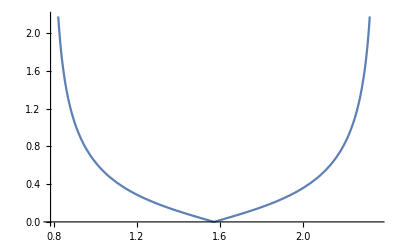

```mathematica
Plot[thetaFuncPrime[x], {x, Pi/4, 3Pi/4}]
```

```mathematica
Integrate[thetaFuncPrime[x], {x, Pi/4, 3Pi/4}]
```

1

```mathematica
D[thetaFunc[phi], phi]
```

-(2 Cot[phi] Csc[phi]^2)/(π √(1-Cot[phi]^4))

```mathematica
InverseFunction[thetaFunc]
```

-ArcCot[√Sin[1/2 π (-1+2 #1)]]&

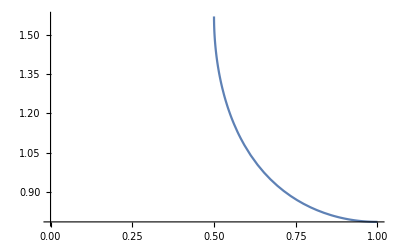

```mathematica
Plot[ArcCot[Sqrt[Sin[1/2 * Pi * (-1 + 2 * x)]]], {x, 0, 1}]
```

```mathematica
phiFunc[theta_] := ArcCot[√Sin[1/2 π (-1+2 *theta)]]
```

```mathematica
Plot[phiFunc[x], {x, 0, 1}]
```

-Graphics-

```mathematica
phiFuncPrime[thetaStar_] := Abs[D[phiFunc[theta], theta]]/.{theta->thetaStar}
```

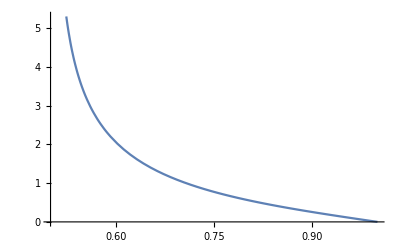

```mathematica
Plot[phiFuncPrime[x], {x, 0.5, 1}]
```

```mathematica
D[phiFunc[theta], theta]
```

-(π Cos[1/2 π (-1+2 theta)])/(2 √Sin[1/2 π (-1+2 theta)] (1+Sin[1/2 π (-1+2 theta)]))